If you find this useful, please cite Kesava, Sameer Vajjala; Department of Physics, University of Oxford.

```mathematica
SetDirectory["/home/sameer/Dropbox/Oxford Projects/Link to Documents/Work with Ivan"] (*Set the working directory*)
```

/home/sameer/Dropbox/Oxford Projects/Link to Documents/Work with Ivan

```mathematica
Data = Import["TAPC5pc12hrsUVdim.xlsx", {"Data",1}]; (*Import Transmittance data from excel*)
```

```mathematica
Data[[1]] (*Should be of the format {wavelength in nm, Transmittance}*)
```

{210.,0.85457}

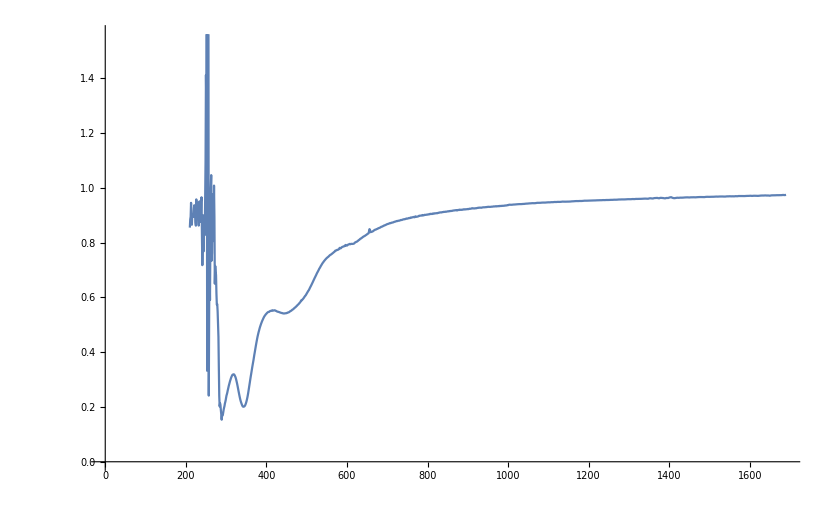

```mathematica
ListLinePlot[Data]
```

```mathematica
Data2 = Drop[Data, 70]; (*Filtering out unphysical data points by choosing a reasonable starting point*)
Data2[[1]]
```

{280.,0.50162}

```mathematica
TrData =Transpose[Data2];
```

#### Constants

```mathematica
thickness = 50 (* thickness of the film in nm*);
h = 6.626*10^(-34);
c = 3*10^(8);
q = 1.602*10^(-19);
```

#### Converting data into extinction coefficient

```mathematica
TrData⟦2⟧=-(Log[TrData⟦2⟧] TrData⟦1⟧)/(thickness (4 π)); (*Converting Transmittance into k*)
```

```mathematica
TrData[[1]] = (c*h)/(q*TrData[[1]]*10^(-9)); (*Converting nm into eV*)
```

```mathematica
FinalData = Sort[Transpose[TrData], #1[[1]]<#2[[1]]&];
```

#### Plotting extinction coefficient derived from Transmittance/Absorbance data

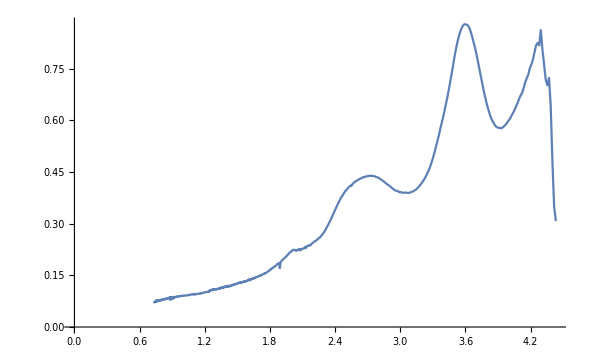

```mathematica
ListLinePlot[FinalData]
```

```mathematica
Plotdata=FinalData;
```

```mathematica
Plotdata[[1]]
```

{0.734215,0.0706922}

```mathematica
Plotdata[[1,2]]
```

0.0706922

## Using a combination (will vary with material) of Lorentz and TaucLorentz functions to fit to the k data

```mathematica
Lorentz[x_,k_,ω0_,Γ_]:=(Γ k x)/(Γ^2 x^2+(ω0^2-x^2)^2);
```

```mathematica
TaucLorentz[x_,k_,ω0_,Γ_,Eg_]:=(ω0 Γ k (x-Eg)^2)/((Γ^2 x^2+(x^2-ω0^2)^2) x);
```

```mathematica
fit1 = NonlinearModelFit[Plotdata,{Lorentz[x, k1,ω01,Γ1] + Lorentz[x, k2,ω02,Γ2]+Lorentz[x, k3,ω03,Γ3] +TaucLorentz[x, k4,ω04,Γ4,ωg4]+Lorentz[x, k5,ω05,Γ5], ω01>0,k1>0, ω02>0, k2>0,ω03>0,k3>0, ω04>0, k4>0,ωg4>0,ω05>0, k5>0}, {{k1,0.001},{ω01,4.3},{Γ1, 0.414},(*{ωg1,0.8},*) { k2,0.3},{ω02,2.7} ,{Γ2,1},(*{ωg2,2},*){k3,0.6},{ω03,3.6},{Γ3,0.5},(* {ωg3,3},*){k4,0.15}, {ω04,2.24},{Γ4,2},{ωg4,1},{k5,0.15},{ω05,2},{Γ5, 1.5}},x, MaxIterations->100000]
```

FittedModel[(2.08869 x)/(16.1946 x^2+(4.8678-x^2)^2)+(0.666893 x)/(0.757273 x^2+(«18»-«1»)^2)+(«19»«1»«1»)/(«1»+«1»)+(0.510254 x)/(«20» x^2+(«1»)^2)+(0.00546489 (-0.000366556+x)^2)/(x (0.0771182 x^2+(-3.9186+x^2)^2))]

```mathematica
fit1["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
k1 | 1.20319 | 0.0412467 | 29.1705 | 3.3919×10^-135
ω01 | 4.25303 | 0.00150019 | 2834.99 | 6.92391093497×10^-1922
Γ1 | 0.424086 | 0.00840526 | 50.4548 | 8.06691×10^-275
k2 | 0.766355 | 0.0941377 | 8.14078 | 1.18426×10^-15
ω02 | 2.7057 | 0.00448966 | 602.651 | 1.00284567021×10^-1262
Γ2 | 0.870214 | 0.0460786 | 18.8854 | 4.29507×10^-68
k3 | 1.42605 | 0.0465256 | 30.6509 | 2.89812×10^-145
ω03 | 3.61177 | 0.00139289 | 2593. | 7.05165499924×10^-1884
Γ3 | 0.548002 | 0.0090314 | 60.6774 | 2.52289942145×10^-334
k4 | 0.00994118 | 0.0356191 | 0.279097 | 0.780229
ω04 | 1.97954 | 0.0261032 | 75.8352 | 1.41195146905×10^-412
Γ4 | 0.277702 | 0.047991 | 5.78654 | 9.65987×10^-9
ωg4 | 0.000366556 | 3.65843 | 0.000100195 | 0.99992
k5 | 0.519026 | 0.522153 | 0.994012 | 0.320462
ω05 | 2.20631 | 0.837691 | 2.6338 | 0.00857648
Γ5 | 4.02425 | 2.53885 | 1.58507 | 0.113273

```mathematica
fit1["BestFitParameters"]
```

{k1→1.20319,ω01→4.25303,Γ1→0.424086,k2→0.766355,ω02→2.7057,Γ2→0.870214,k3→1.42605,ω03→3.61177,Γ3→0.548002,k4→0.00994118,ω04→1.97954,Γ4→0.277702,ωg4→0.000366556,k5→0.519026,ω05→2.20631,Γ5→4.02425}

```mathematica
fit1["RSquared"]
```

0.998503

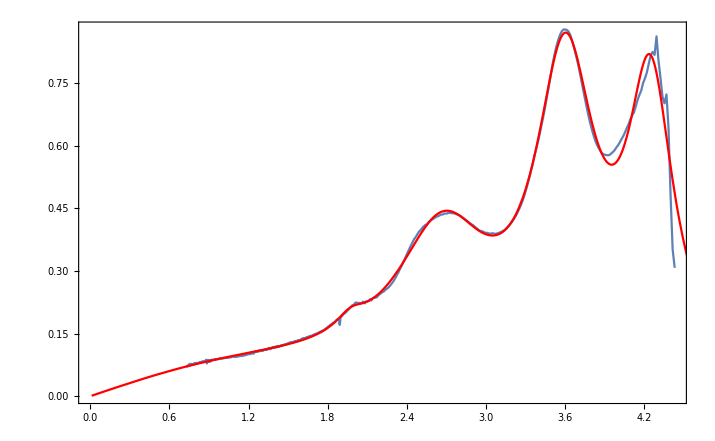

```mathematica
Plot1 = Show[ListLinePlot[Plotdata], Plot[fit1[x], {x, 0.01,20}, PlotStyle->Red, PlotRange->All], Frame->True ]
```

```mathematica
K1 = k1/.fit1["BestFitParameters"];
W1 = ω01/.fit1["BestFitParameters"];
T1 = Γ1/.fit1["BestFitParameters"];
(*Wg1 = ωg1/.fit1["BestFitParameters"];*)
K2 = k2/.fit1["BestFitParameters"];
W2 = ω02/.fit1["BestFitParameters"];
T2 = Γ2/.fit1["BestFitParameters"];
K3 = k3/.fit1["BestFitParameters"];
W3= ω03/.fit1["BestFitParameters"];
T3= Γ3/.fit1["BestFitParameters"];
K4 = k4/.fit1["BestFitParameters"];
W4= ω04/.fit1["BestFitParameters"];
T4= Γ4/.fit1["BestFitParameters"];
Wg4 = ωg4/.fit1["BestFitParameters"];
K5 = k5/.fit1["BestFitParameters"];
W5 = ω05/.fit1["BestFitParameters"];
T5 = Γ5/.fit1["BestFitParameters"];
```

Copy the parameter values into a set of constants

## Equation for Dispersion n derived from Kramers-Kronig equation

### n for TaucLorentz

```mathematica
α[ω0_,Γ_]:=√(4 ω0^2-Γ^2);
γ[ω0_,Γ_]:=√(ω0^2-Γ^2/2);
ζ[x_,ω0_,Γ_]:=(x^2-γ[ω0,Γ]^2)^2+1/4 α[ω0,Γ]^2 Γ^2;
```

```mathematica
nTaucLorentz[x_,k_,ω0_,Γ_,ωg_]:=(k Γ ((ωg^2-ω0^2) x^2+ωg^2 Γ^2-ω0^2 (ω0^2+3 ωg^2)) Log[(ω0^2+ωg^2+α[ω0,Γ] ωg)/(ω0^2+ωg^2-α[ω0,Γ] ωg)])/(π ζ[x,ω0,Γ] 2 α[ω0,Γ] ω0)-(k ((x^2-ω0^2) (ω0^2+ωg^2)+ωg^2 Γ^2) (π-ArcTan[(2 ωg+α[ω0,Γ])/Γ]+ArcTan[(-2 ωg+α[ω0,Γ])/Γ]))/(π ζ[x,ω0,Γ] ω0)+(2 k ω0 ωg (x^2-γ[ω0,Γ]^2) (π+2 ArcTan[(2 (γ[ω0,Γ]^2-ωg^2))/(α[ω0,Γ] Γ)]))/(π ζ[x,ω0,Γ] α[ω0,Γ])-(k ω0 Γ (x^2+ωg^2) Log[Abs[x-ωg]/(x+ωg)])/(π ζ[x,ω0,Γ] x)+(2 k ω0 Γ ωg Log[(Abs[x-ωg] (x+ωg))/(√((ω0^2+ωg^2)^2+ωg^2 Γ^2))])/(π ζ[x,ω0,Γ]);
```

### n for Lorentz

```mathematica
nLorentz[x_,k_,ω0_,Γ_]:=(k (ω0^2-x^2))/((x^2-ω0^2)^2+Γ^2 x^2);
```

### Final equation for n using the above fitted functions

```mathematica
n∞ = 2;
```

Have to add n∞ manually, choosing a value of 2 for organic semiconductors

```mathematica
Finaln[x_]:=n∞+nLorentz[x, K1,W1,T1] + nLorentz[x, K2,W2,T2]+nLorentz[x, K3,W3, T3] +nTaucLorentz[x, K4, W4, T4,Wg4]+nLorentz[x, K5,W5,T5];
```

Use the above combination of functions to obtain n

### Plotting n without n∞

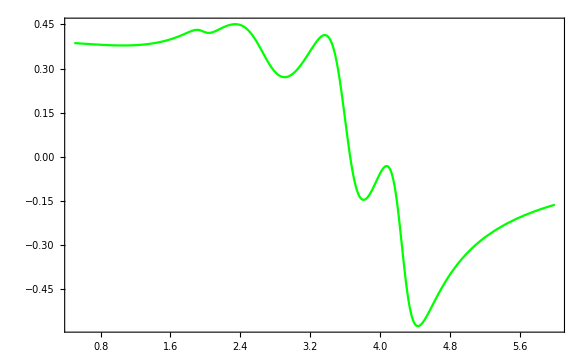

```mathematica
Plot[Finaln[x]- n∞, {x, 0.5,6}, Frame-> True, PlotRange-> All, PlotStyle->Green]
```

### Plotting n with n∞

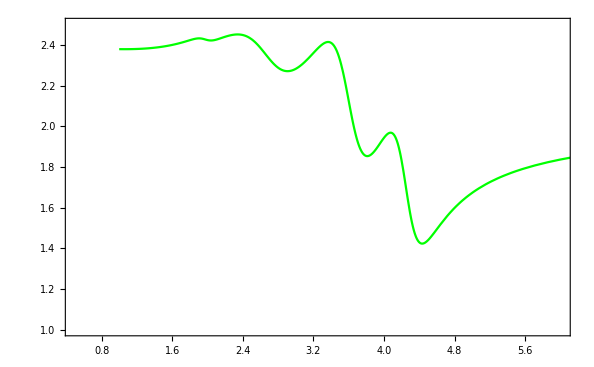

```mathematica
Plot2=Plot[Finaln[x], {x, 1,8}, Frame-> True, PlotRange-> {{0.5,6},{1,2.5}}, PlotStyle->Green]
```

## Plotting All

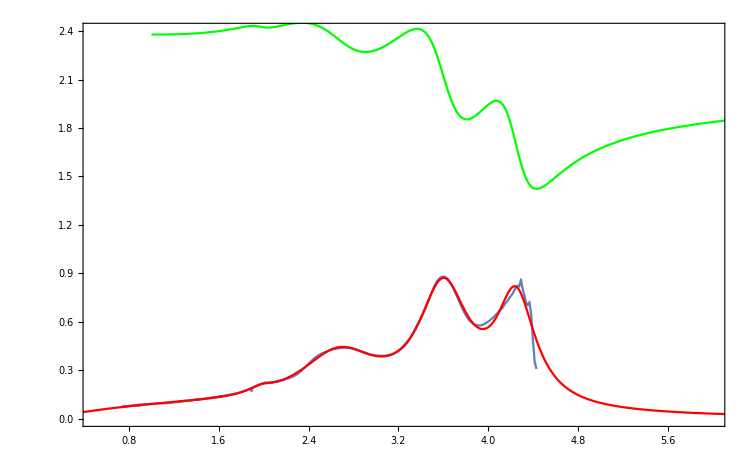

```mathematica
Show[Plot1,Plot2, PlotRange->{{0.5,6},{0,2.4}}]
```

## Exporting Data

```mathematica
Exportdata = Table[{h*c/(q*Plotdata[[i,1]]*10^(-9)),Finaln[Plotdata[[i,1]]],fit2[Plotdata[[i,1]]], Plotdata[[i,2]]},{i,1,Length[Plotdata]}];
```

```mathematica
Export["Refractive_Index.xlsx",Join[{{"Wavelength (nm)", "n_KK", "k_fit", "k_data"}},Exportdata]];
```